```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

## n \mapsto t[n] is defined as a table in myFunctionsPureCodeV8 copy.nb, whhich is loaded by myFunctionsMathematica8.m. The table was created in my2ndEditOdlyzkoAccrtZrs6dec15.nb. It is from a table on Odlyzko’s site.

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

_______________________________________________

Riemann zero   1

iterate bound  241

spirals from fixed point  1 for Riemann zero   1

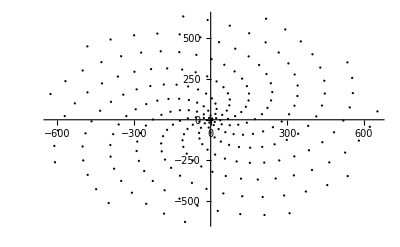

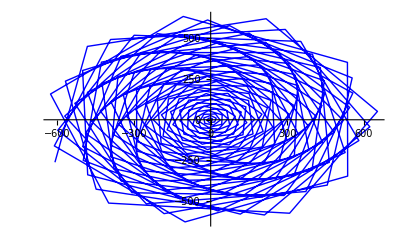

log r vs. theta

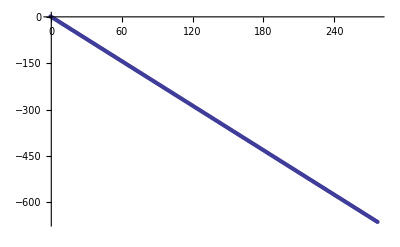

first {slope, intercept}

{-2.394847979191633357822268522625423824759083662298882616214462020101713057742667116356786817603471408859540708669297586735444142286634084185088759217885793902974232400074521370866781504296602398374091275781654186562920655122102940384875769486595381378902623787602214,0.06107288039806658180872472692653010747963614414004701165883691949722665173551175243248248601318455210167846213430427083407413319871893291786466994492431134387205380452198276577193801887681671599190886508625360658331917704748768811397385902711280894829230367696171}

second {slope, intercept}

{-2.394847979191633357822268133633419152411506150311825846280357303020498313753054690087176694460587895872050958377355449782617689201863235366908690372333947819646967230659539348436938665295241855982919436046,0.0610728803980665818087118982854440933271383022274808681108136383619548509916965900343579143748859594056185378775912502970586797516917380527619494956868092863509670863215722631033953705753789277532404663}

arg increments for Riemann zero   1

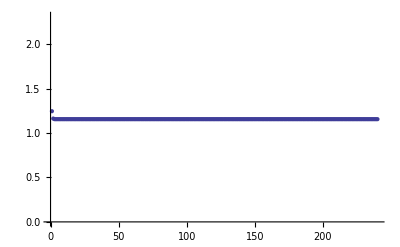

height of the last point in above plot:

1.155855786

log |arg increment increments| for Riemann zero   1

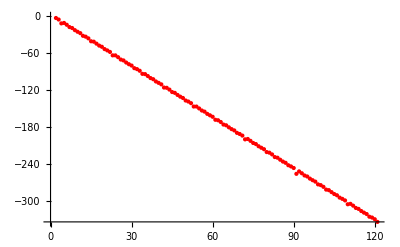

first {slope, intercept}

{-2.8778191532842486830540200007031292127205016924309060099415243778511409927072602467549824139191900678331133214333405906602900502500652093501433070311289924628950101982201524423582266432936652177542547173207661848948340199612158,5.355544729369974438974368576820227600841517466537776542016997219402692463299393050289803867593575263643085160141630902036626940843493717796813281502158027178491112874230097489416598869066647932884661449568827007015528943839722}

second {slope, intercept}

{-2.7744972056466933891107754101850788244121380267876237011666338887645810824129845722185535001990110210092939,3.76226214292119869908759954354925449045700079951108386516052951869811574559984077703820163215640692067479}

logarithmic spiral c vs b

```mathematica
stream=OpenRead["zeta1fixedpts13dec15"];
ls=ReadList[stream];
Close[stream];
stream2=OpenWrite["NtoNzrs1jan16no2"];
f[n_,zr_]:=Block[{$MinPrecision=300},1+Floor[Log[Abs[zetaIterate[zr,n]]]]];
For[n=0,n<100,n++;
Print["_______________________________________________"];
Print["Riemann zero   ",n];
precision=300;
polardata={};
polardata2={};
logspiralsolutions1={};
logspiralsolutions2={};
logspiralsolutions3={};
fx=ls[[n,2]];
zr=bestzero[n];
zeros={zr};
la=Re[Log[Abs[zr-fx]]];
arg=Arg[zr-fx];
args={arg};
polardata=Append[polardata,{la*Cos[arg],la*Sin[arg]}];
polardata2=Append[polardata2,{arg,la}];
theta1=polardata2[[1,1]];
la1=polardata2[[1,2]];

For[k=1,k<300,k++;
startcenter=fx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision,WorkingPrecision->precision][[1,2]];
zeros=Append[zeros,zr];
la=Re[Log[Abs[zr-fx]]];
arg=Arg[zr-fx];
While[Not[arg>Last[args]],arg=arg+2*Pi];
args=Append[args,arg];
polardata=Append[polardata,{la*Cos[arg],la*Sin[arg]}];
polardata2=Append[polardata2,{arg,la}];

];(*end k loop *)




bound=0;
For[m=0,m<300,m++;
zr=zeros[[m]];
error=f[m,zr];
If[error<-12,Write[stream2,{n,m,zeros[[m]],error}];
theta2=polardata2[[m,1]];
la2=polardata2[[m,2]];
If[Not[Det[{{la1,theta1},{la2,theta2}}]==0],
solve=Solve[{la1==u*theta1+v,la2==u*theta2+v},{u,v}];
b=solve[[1,1,2]];
c=solve[[1,2,2]];
logspiralsolutions1=Append[logspiralsolutions1,{b,c}];
logspiralsolutions2=Append[logspiralsolutions2,{m,b}];
logspiralsolutions3=Append[logspiralsolutions3,{m,c}];
];
bound++];
If[Not[error<-12],Break[]]];
(*end m loop *)
Print["iterate bound  ",bound];





argdiffs={};.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10
For[kk=1,kk<bound,kk++;
argdiffs=
Append[argdiffs,args[[kk]]-args[[kk-1]]]
];(* end kk loop *)
argdiffdiffs={};
For[kkk=1,kkk<bound-1,kkk++;
argdiffdiff={kkk,Log[Abs[argdiffs[[kkk]]-argdiffs[[kkk-1]]]]};
argdiffdiffs=Append[argdiffdiffs,argdiffdiff];
];(* end kkk loop *)

Print["spirals from fixed point  ",n," for Riemann zero   ",n];

Print[ListPlot[polardata,PlotStyle->{Black,PointSize[.004]}]];
Print[ListPlot[polardata,Joined->True,PlotStyle->Blue]];
Print["log r vs. theta"];
Print[ListPlot[polardata2]];
Print["first {slope, intercept}"];
Print[lineFromPoints4[Part[polardata2,20;;30]]];
Print["second {slope, intercept}"];
Print[lineFromPoints4[Part[polardata2,70;;80]]];
Print["arg increments for Riemann zero   ",n];
Print[ListPlot[argdiffs]];
Print["height of the last point in above plot:"];
Print[Last[argdiffs]];
Print["log |arg increment increments| for Riemann zero   ",n];
Print[ListPlot[argdiffdiffs,PlotStyle->Red]];
Print["first {slope, intercept}"];
Print[lineFromPoints4[Part[argdiffdiffs,20;;30]]];
Print["second {slope, intercept}"];
Print[lineFromPoints4[Part[argdiffdiffs,70;;80]]];
Print["logarithmic spiral c vs b"];
Print[ListPlot[logspiralsolutions1,PlotStyle->Blue]];
Print["logarithmic spiral b vs m"];
Print[ListPlot[logspiralsolutions2,PlotStyle->Blue]];
Print["logarithmic spiral c vs m"];
Print[ListPlot[logspiralsolutions3,PlotStyle->Blue]];
]; (* end n loop *)
Close[stream2]
```

## leaf5point6left

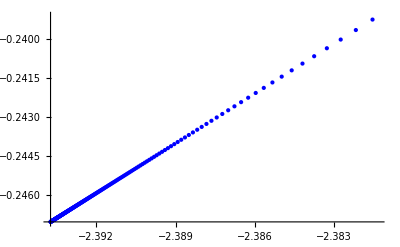

logarithmic spiral b vs m

## leaf5point6center

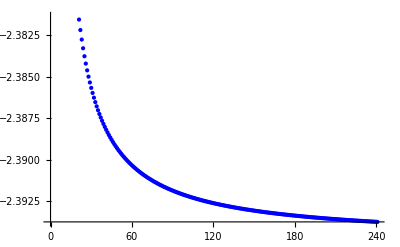

logarithmic spiral c vs m

## leaf5point6right

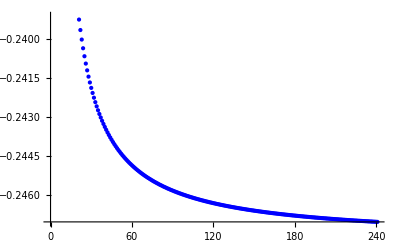

_______________________________________________

Riemann zero   2

iterate bound  195

spirals from fixed point  2 for Riemann zero   2

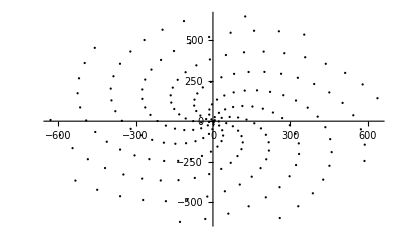

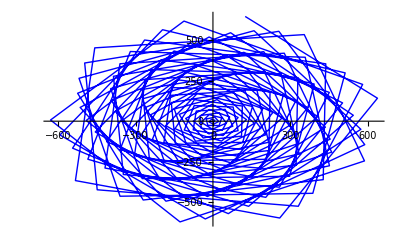

log r vs. theta

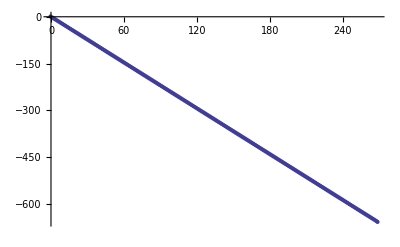

first {slope, intercept}

{-2.4452200140731494125342279617193865862607043302870493955934322338503108504353572283688071372854927348067362892016163776748526612448449144430737322581949484796988762279050999811911236839501213285282296531994774469971164092423307126437900980746969972640044489,0.270185665707392861349871915625425111365744606698087776031525458901595293440610491464223694281201416783857323133494041226341543503075879670784186352635486995622910343190343589353369931464899791053517082934887902634311017054411379350267225447050709456851628}

second {slope, intercept}

{-2.445220014073149412534227961720197205903916918675544267556551491827112193777557079435456825154770445800503459196081308717851749329267076640646210519978250883505394598825944565956392664,0.2701856657073928613498719156575975772651763100823579055376845935193468643046343004129168269982596608340338933690692902288164007910866680804939357607276449361284664230486384773819187}

arg increments for Riemann zero   2

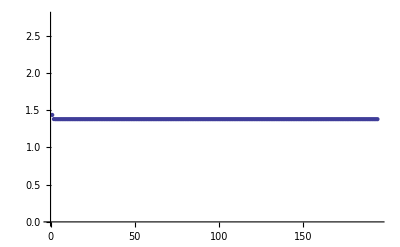

height of the last point in above plot:

1.37917995685849

log |arg increment increments| for Riemann zero   2

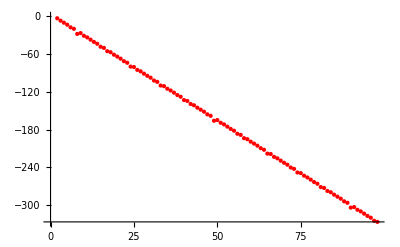

first {slope, intercept}

{-3.473329272951094837015467186883474095708147599720496875127647746726063336410991659728486629218677534290310305792806637342264423798268486513593359918319187961715591287877808227831333228923209730692641128439846774,5.85722651172834294428404032690009121322219243140295420741825589193588032166334321238957089299028649132631290860429415908936115818807668625683163435357838780579336427431133958108931471152972535999810239819040423}

second {slope, intercept}

{-3.556870087955719176117348577428397373249647024416688514371724191,16.9340704981938886018469180820308645128061772696901908984040122}

logarithmic spiral c vs b

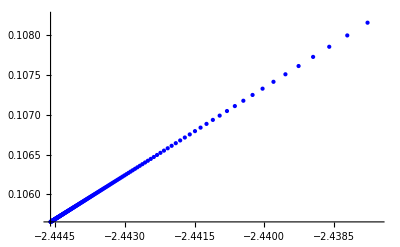

logarithmic spiral b vs m

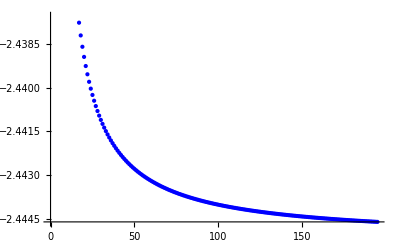

logarithmic spiral c vs m

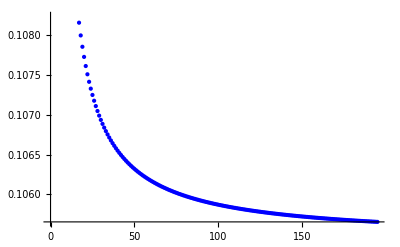

_______________________________________________

Riemann zero   3

$Aborted